Jacobians and Eigen analysis

```mathematica
Clear["Global`*"]
```

Disease impacts JUVENILE stage

```mathematica
(* Equations *)
eqJS:=JS'[t]==f A[t]-(m0S-mbS*(JS[t]+JI[t]))*JS[t]-uJ JS[t]-betaJ JS[t]*JI[t];

eqJI:=JI'[t]==betaJ JS[t]*JI[t]-(m0I-mbI (JS[t]+JI[t]))*JI[t]-(uJ+alphaJ)*JI[t];

eqA:=A'[t]==(m0S-mbS (JS[t]+JI[t]))*JS[t]+(m0I-mbI (JS[t]+JI[t]))*JI[t]-uA A[t]; 

eqsol1=FullSimplify[Solve[{eqJS[[2]]==0,eqJI[[2]]==0,eqA[[2]]==0},{JS[t],JI[t],A[t] }]];
eqsol1[[1]]
eqsol1[[2]]
eqsol1[[3]];
eqsol1[[4]];
(* Jacobian *)
Jac1 := ({{D[eqJS[[2]],JS[t]], D[eqJS[[2]],JI[t]], D[eqJS[[2]],A[t]]}, {D[eqJI[[2]],JS[t]], D[eqJI[[2]],JI[t]], D[eqJI[[2]],A[t]]}, {D[eqA[[2]],JS[t]], D[eqA[[2]],JI[t]], D[eqA[[2]],A[t]]}})
MatrixForm[Jac1]
```

{JS[t]→0,JI[t]→0,A[t]→0}

{JS[t]→(f m0S-uA (m0S+uJ))/(mbS (f-uA)),JI[t]→0,A[t]→(f m0S uJ-uA uJ (m0S+uJ))/(mbS (f-uA)^2)}

(-m0S-uJ-betaJ JI[t]+mbS JS[t]+mbS (JI[t]+JS[t]) | -betaJ JS[t]+mbS JS[t] | f
betaJ JI[t]+mbI JI[t] | -alphaJ-m0I-uJ+mbI JI[t]+betaJ JS[t]+mbI (JI[t]+JS[t]) | 0
m0S-mbI JI[t]-mbS JS[t]-mbS (JI[t]+JS[t]) | m0I-mbI JI[t]-mbS JS[t]-mbI (JI[t]+JS[t]) | -uA)

```mathematica
(* Equations *)
eqJS2:=JS2'[t]==f A2[t]-(m0S-mbS*(JS2[t]+JI2[t]))*JS2[t]-uJ JS2[t]-betaJ JS2[t]*JI2[t];

eqJI2:=JI2'[t]==betaJ JS2[t]*JI2[t]-(uJ+alphaJ)*JI2[t];

eqA2:=A2'[t]==(m0S-mbS (JS2[t]+JI2[t]))*JS2[t]-uA A2[t]; 

eqsol2=FullSimplify[Solve[{eqJS2[[2]]==0,eqJI2[[2]]==0,eqA2[[2]]==0},{JS2[t],JI2[t],A2[t] }]];
eqsol2[[1]]
eqsol2[[2]]
eqsol2[[3]]
(* Jacobian *)
Jac2 := ({{D[eqJS2[[2]],JS2[t]], D[eqJS2[[2]],JI2[t]], D[eqJS2[[2]],A2[t]]}, {D[eqJI2[[2]],JS2[t]], D[eqJI2[[2]],JI2[t]], D[eqJI2[[2]],A2[t]]}, {D[eqA2[[2]],JS2[t]], D[eqA2[[2]],JI2[t]], D[eqA2[[2]],A2[t]]}})
MatrixForm[Jac2]
```

{JS2[t]→0,JI2[t]→0,A2[t]→0}

{JS2[t]→(alphaJ+uJ)/betaJ,JI2[t]→(betaJ f m0S-mbS (f-uA) (alphaJ+uJ)-betaJ uA (m0S+uJ))/(betaJ (f mbS+(betaJ-mbS) uA)),A2[t]→((betaJ m0S-alphaJ mbS) (alphaJ+uJ))/(betaJ (f mbS+(betaJ-mbS) uA))}

{JS2[t]→(f m0S-uA (m0S+uJ))/(mbS (f-uA)),JI2[t]→0,A2[t]→(f m0S uJ-uA uJ (m0S+uJ))/(mbS (f-uA)^2)}

(-m0S-uJ-betaJ JI2[t]+mbS JS2[t]+mbS (JI2[t]+JS2[t]) | -betaJ JS2[t]+mbS JS2[t] | f
betaJ JI2[t] | -alphaJ-uJ+betaJ JS2[t] | 0
m0S-mbS JS2[t]-mbS (JI2[t]+JS2[t]) | -mbS JS2[t] | -uA)

```mathematica
Coeff2 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac1/.eqsol1[[2]],X],X]]
a0Eq2:=Coeff2[[1]]/Coeff2[[4]]
a1Eq2:=Coeff2[[2]]/Coeff2[[4]]
a2Eq2:=Coeff2[[3]]/Coeff2[[4]]
a3Eq2:=Coeff2[[4]]/Coeff2[[4]]

Coeff3 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac1/.eqsol1[[3]],X],X]]
a0Eq3:=Coeff3[[1]]/Coeff3[[4]]
a1Eq3:=Coeff3[[2]]/Coeff3[[4]]
a2Eq3:=Coeff3[[3]]/Coeff3[[4]]
a3Eq3:=Coeff3[[4]]/Coeff3[[4]]

Coeff4 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac1/.eqsol1[[4]],X],X]]
a0Eq4:=Coeff4[[1]]/Coeff4[[4]]
a1Eq4:=Coeff4[[2]]/Coeff4[[4]]
a2Eq4:=Coeff4[[3]]/Coeff4[[4]]
a3Eq4:=Coeff4[[4]]/Coeff4[[4]]
RH1Eq2:=a0Eq2>0&&a2Eq2>0&&a2Eq2*a1Eq2-a0Eq2>0
RH1Eq3:=a0Eq3>0&&a2Eq3>0&&a2Eq3*a1Eq3-a0Eq3>0
RH1Eq4:=a0Eq4>0&&a2Eq4>0&&a2Eq4*a1Eq4-a0Eq4>0

Coeff22 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac2/.eqsol2[[3]],X],X]]
a0Eq22:=Coeff22[[1]]/Coeff22[[4]]
a1Eq22:=Coeff22[[2]]/Coeff22[[4]]
a2Eq22:=Coeff22[[3]]/Coeff22[[4]]
a3Eq22:=Coeff22[[4]]/Coeff22[[4]]

Coeff32 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac2/.eqsol2[[2]],X],X]]
a0Eq32:=Coeff32[[1]]/Coeff32[[4]]
a1Eq32:=Coeff32[[2]]/Coeff32[[4]]
a2Eq32:=Coeff32[[3]]/Coeff32[[4]]
a3Eq32:=Coeff32[[4]]/Coeff32[[4]]
RH2Eq2:=a0Eq22>0&&a2Eq22>0&&a2Eq22*a1Eq22-a0Eq22>0
RH2Eq3:=a0Eq32>0&&a2Eq32>0&&a2Eq32*a1Eq32-a0Eq32>0
```

```mathematica
feasible1Eq2:=Element[eqsol1[[2]][[1]][[2]],PositiveReals]&&Element[eqsol1[[2]][[3]][[2]],PositiveReals];
feasible1Eq3:=Element[eqsol1[[3]][[1]][[2]],PositiveReals]&&Element[eqsol1[[3]][[2]][[2]],PositiveReals]&&Element[eqsol1[[3]][[3]][[2]],PositiveReals];
feasible1Eq4:=Element[eqsol1[[4]][[1]][[2]],PositiveReals]&&Element[eqsol1[[4]][[2]][[2]],PositiveReals]&&Element[eqsol1[[4]][[3]][[2]],PositiveReals];
feasible2Eq2:=Element[eqsol2[[3]][[1]][[2]],PositiveReals]&&Element[eqsol2[[3]][[3]][[2]],PositiveReals];
feasible2Eq3:=Element[eqsol2[[2]][[1]][[2]],PositiveReals]&&Element[eqsol2[[2]][[2]][[2]],PositiveReals]&&Element[eqsol2[[2]][[3]][[2]],PositiveReals];

Stable1Eq2:=(feasible1Eq2)&&(RH1Eq2)
Stable1Eq3:=(feasible1Eq3)&&(RH1Eq3)
Stable1Eq4:=(feasible1Eq4)&&(RH1Eq4)
Unstable1Eq3:=(feasible1Eq3)&&(!RH1Eq3)
Unstable1Eq4:=(feasible1Eq4)&&(!RH1Eq4)
Stable2Eq3:=(feasible2Eq3)&&(RH2Eq3)
Unstable2Eq3:=(feasible2Eq3)&&(!RH2Eq3)
Stable:=(Stable1Eq3)||(Stable2Eq3)
Unstable:=(!Stable1Eq3)&&(!Stable2Eq3)
```

Figure 2B

Figure 2B

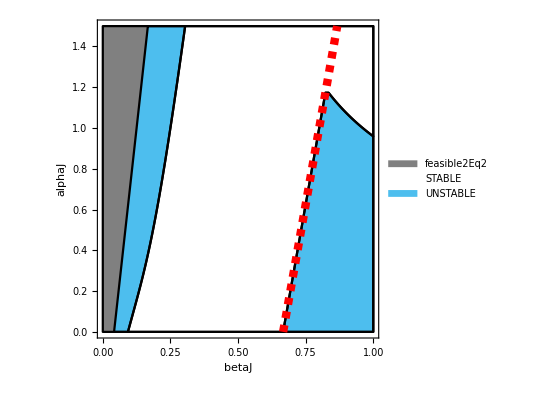

```mathematica
f=3;
uJ=0.5;
m0S=2.5;
uA=0.5; (* 0.5*)
mbS=0.2;
mbI=0.2;
m0I=1.5;

MatIssue3:=(eqsol1[[3]][[1]][[2]]+eqsol1[[3]][[2]][[2]])> m0I/mbI
STABLE1eq3:=(!MatIssue3)&&(Stable1Eq3)
STABLE2eq3:=(MatIssue3)&&(Stable2Eq3)
STABLE:=((!MatIssue3)&&(Stable1Eq3))||((MatIssue3)&&(Stable2Eq3))
(* UNSTABLE1eq3:=(!MatIssue3)&&(!Stable1Eq3)
UNSTABLE2eq3:=(!MatIssue3)&&(!Stable2Eq3)
UNSTABLE:=(UNSTABLE1eq3)||(UNSTABLE2eq3)||(UNSTABLE1eq3&&UNSTABLE2eq3) *)
UNSTABLE:=((!MatIssue3)&&(Unstable1Eq3))||((MatIssue3)&&(Unstable2Eq3))
Thresh=Line[{{0.666667,0},{0.866667,1.5}}];
(*CRegionPlot[{feasible2Eq2,STABLE, UNSTABLE},{betaJ,0,1.0}, {alphaJ, 0, 3*uJ}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large,Epilog->{Red,Thickness[0.01],Dashed,Thresh}] *)

"Figure 2B"
RegionPlot[{feasible2Eq2,STABLE, UNSTABLE},{betaJ,0,1.0}, {alphaJ, 0, 3*uJ}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933]},BoundaryStyle->{Black},Epilog->{Red,Thickness[0.015],Dashed,Thresh}]
```

Figure 2C

Figure 2C

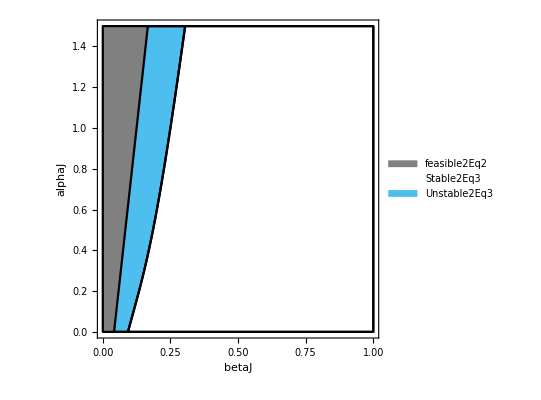

```mathematica
f=3;
uJ=0.5;
m0S=2.5;
uA=0.5; (* 0.5*)
mbS=0.2;
mbI=0;
m0I=0;

"Figure 2C"
RegionPlot[{feasible2Eq2,Stable2Eq3, Unstable2Eq3},{betaJ,0,1.0}, {alphaJ, 0, 3*uJ}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933]},BoundaryStyle->{Black}]
```